149668992000

5005060000

1.03401

0.0167204

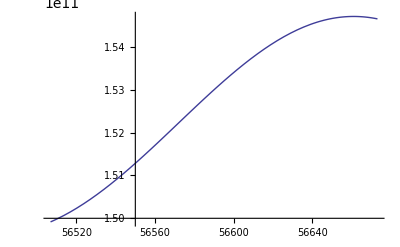

0.+0.263013 ⅈ

```mathematica
Remove["Global`*"]
a = 152171522000;
b = 147166462000;
(*The 2013 perihelion is around 05:00 UTC on January 2,2013 and the aphelion is around July 5,2013 at 15:00 UTC.In 2014 the perihelion is around 12:00 UTC on January 4,2014 and the aphelion is around 00:00 on July 4,2014.*)
(a-b)/2+b
(a-b)
N[a/b]
ϵ=√(1-(a/b)^2);
N[e=1-2/(a/b+1)]
r[t_] := (a(1-e^2))/(1+e Cos[(2π)/365(t-56478.5)])
Plot[r[t],{t,56506.8942593,56673.095347}]
N[ϵ]
```